# CS 298 - Lab 6

## Kyle Perra

## Euler’s Method - Part 1

0 | 100 | 100 | 0
2 | 120. | 122.14 | 0.0175231
4 | 144. | 149.182 | 0.0347391
6 | 172.8 | 182.212 | 0.0516535
8 | 207.36 | 222.554 | 0.0682715
10 | 248.832 | 271.828 | 0.0845982
12 | 298.598 | 332.012 | 0.100639
14 | 358.318 | 405.52 | 0.116398
16 | 429.982 | 495.303 | 0.131882
18 | 515.978 | 604.965 | 0.147094
20 | 619.174 | 738.906 | 0.16204

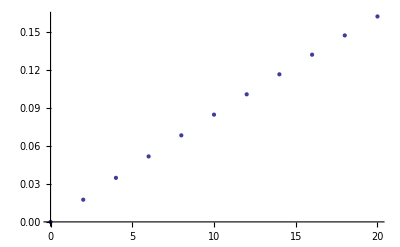

```mathematica
Clear[dP];
dP[P_] := 0.1P;
P=100;
deltaT =2;
numIterations = 10;
exactP=P;
dataTable = {{0,P,exactP,0}};
Do[
t=i*deltaT;
P=P +dP[P] * deltaT;
exactP = 100 E^(0.1t);
dataTable = Append[dataTable,{t,P,exactP, Abs[P-exactP]/exactP}],{i,numIterations}]
TableForm[dataTable]
values= dataTable[[All,{1,4}]];
ListPlot[values]
```

## Euler’s Method - Part 2

0 | 100 | 100 | 0
0.25 | 102.5 | 102.532 | 0.00030734
0.5 | 105.063 | 105.127 | 0.000614586
0.75 | 107.689 | 107.788 | 0.000921737
1. | 110.381 | 110.517 | 0.00122879
1.25 | 113.141 | 113.315 | 0.00153576
1.5 | 115.969 | 116.183 | 0.00184262
1.75 | 118.869 | 119.125 | 0.0021494
2. | 121.84 | 122.14 | 0.00245608
2.25 | 124.886 | 125.232 | 0.00276266
2.5 | 128.008 | 128.403 | 0.00306915
2.75 | 131.209 | 131.653 | 0.00337555
3. | 134.489 | 134.986 | 0.00368185
3.25 | 137.851 | 138.403 | 0.00398806
3.5 | 141.297 | 141.907 | 0.00429418
3.75 | 144.83 | 145.499 | 0.0046002
4. | 148.451 | 149.182 | 0.00490612
4.25 | 152.162 | 152.959 | 0.00521196
4.5 | 155.966 | 156.831 | 0.00551769
4.75 | 159.865 | 160.801 | 0.00582334
5. | 163.862 | 164.872 | 0.00612889
5.25 | 167.958 | 169.046 | 0.00643435
5.5 | 172.157 | 173.325 | 0.00673971
5.75 | 176.461 | 177.713 | 0.00704498
6. | 180.873 | 182.212 | 0.00735015
6.25 | 185.394 | 186.825 | 0.00765523
6.5 | 190.029 | 191.554 | 0.00796022
6.75 | 194.78 | 196.403 | 0.00826511
7. | 199.65 | 201.375 | 0.00856991
7.25 | 204.641 | 206.473 | 0.00887462
7.5 | 209.757 | 211.7 | 0.00917923
7.75 | 215.001 | 217.059 | 0.00948375
8. | 220.376 | 222.554 | 0.00978818
8.25 | 225.885 | 228.188 | 0.0100925
8.5 | 231.532 | 233.965 | 0.0103967
8.75 | 237.321 | 239.888 | 0.0107009
9. | 243.254 | 245.96 | 0.0110049
9.25 | 249.335 | 252.187 | 0.0113089
9.5 | 255.568 | 258.571 | 0.0116128
9.75 | 261.957 | 265.117 | 0.0119165
10. | 268.506 | 271.828 | 0.0122202
10.25 | 275.219 | 278.71 | 0.0125238
10.5 | 282.1 | 285.765 | 0.0128273
10.75 | 289.152 | 292.999 | 0.0131307
11. | 296.381 | 300.417 | 0.013434
11.25 | 303.79 | 308.022 | 0.0137372
11.5 | 311.385 | 315.819 | 0.0140403
11.75 | 319.17 | 323.814 | 0.0143433
12. | 327.149 | 332.012 | 0.0146463
12.25 | 335.328 | 340.417 | 0.0149491
12.5 | 343.711 | 349.034 | 0.0152519
12.75 | 352.304 | 357.87 | 0.0155545
13. | 361.111 | 366.93 | 0.0158571
13.25 | 370.139 | 376.219 | 0.0161595
13.5 | 379.392 | 385.743 | 0.0164619
13.75 | 388.877 | 395.508 | 0.0167642
14. | 398.599 | 405.52 | 0.0170664
14.25 | 408.564 | 415.786 | 0.0173685
14.5 | 418.778 | 426.311 | 0.0176705
14.75 | 429.248 | 437.104 | 0.0179724
15. | 439.979 | 448.169 | 0.0182742
15.25 | 450.978 | 459.514 | 0.0185759
15.5 | 462.253 | 471.147 | 0.0188776
15.75 | 473.809 | 483.074 | 0.0191791
16. | 485.654 | 495.303 | 0.0194805
16.25 | 497.796 | 507.842 | 0.0197819
16.5 | 510.241 | 520.698 | 0.0200832
16.75 | 522.997 | 533.88 | 0.0203843
17. | 536.072 | 547.395 | 0.0206854
17.25 | 549.473 | 561.252 | 0.0209864
17.5 | 563.21 | 575.46 | 0.0212873
17.75 | 577.291 | 590.028 | 0.0215881
18. | 591.723 | 604.965 | 0.0218888
18.25 | 606.516 | 620.28 | 0.0221894
18.5 | 621.679 | 635.982 | 0.0224899
18.75 | 637.221 | 652.082 | 0.0227903
19. | 653.151 | 668.589 | 0.0230907
19.25 | 669.48 | 685.515 | 0.0233909
19.5 | 686.217 | 702.869 | 0.0236911
19.75 | 703.372 | 720.662 | 0.0239911
20. | 720.957 | 738.906 | 0.0242911

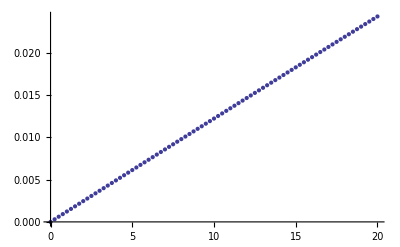

```mathematica
Clear[dP];
dP[P_] := 0.1P;
P=100;
deltaT =0.25;
numIterations = 80;
exactP=P;
dataTable = {{0,P,exactP,0}};
Do[
t=i*deltaT;
P=P +dP[P] * deltaT;
exactP = 100 E^(0.1t);
dataTable = Append[dataTable,{t,P,exactP, Abs[P-exactP]/exactP}],{i,numIterations}]
TableForm[dataTable]
values= dataTable[[All,{1,4}]];
ListPlot[values]
```

The relative error at time 20 is .024

## Runge-Kutta 2

0 | 100 | 100 | 0
2 | 122. | 122.14 | 0.00114848
4 | 148.84 | 149.182 | 0.00229564
6 | 181.585 | 182.212 | 0.00344149
8 | 221.533 | 222.554 | 0.00458602
10 | 270.271 | 271.828 | 0.00572923
12 | 329.73 | 332.012 | 0.00687113
14 | 402.271 | 405.52 | 0.00801172
16 | 490.771 | 495.303 | 0.009151
18 | 598.74 | 604.965 | 0.010289
20 | 730.463 | 738.906 | 0.0114256

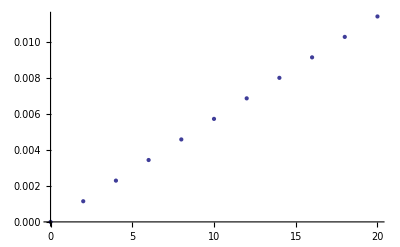

```mathematica
Clear[dP,P,numIterations,deltaT,exactP,dataTable,PredictionPoint];
dP[P_]:=0.1 P;
P=100;
numIterations = 10;
deltaT=2;
exactP=P;
dataTable = {{0,P,exactP,0}};

Do[
t=i * deltaT;
PredictionPoint = P + dP[P]*deltaT;
P=P+0.5*(dP[P]+dP[PredictionPoint])*deltaT;
exactP=100 E^(0.1t);
dataTable = Append[dataTable,{t,P,exactP, Abs[P-exactP]/exactP}],{i,numIterations}]

TableForm[dataTable]
values = dataTable[[All,{1,4}]];
ListPlot[values]
```

The relative error (with Runge Kutta) is .011%
Improvement in methodology: .013